# 2. teden

2. in 3. 3. 2021

## Naloga 1

Izračunaj števili e in π na 1000 decimalk.

```mathematica
N[E,1000]
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427427466391932003059921817413596629043572900334295260595630738132328627943490763233829880753195251019011573834187930702154089149934884167509244761460668082264800168477411853742345442437107539077744992069551702761838606261331384583000752044933826560297606737113200709328709127443747047230696977209310141692836819025515108657463772111252389784425056953696770785449969967946864454905987931636889230098793127736178215424999229576351482208269895193668033182528869398496465105820939239829488793320362509443117301238197068416140397019837679320683282376464804295311802328782509819455815301756717361332069811250996181881593041690351598888519345807273866738589422879228499892086805825749279610484198444363463244968487560233624827041978623209002160990235304369941849146314093431738143640546253152096183690888707016768396424378140592714563549061303107208510383750510115747704171898610687396965521267154688957035035

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

Določi 5., 100. in 443. decimalko števila π.

```mathematica
N[Pi,6]
```

3.14159

```mathematica
N[Pi,101]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
N[Pi,444]
```

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045432664821339360726024914127372458700660631558817488152092096282925409171536436789259036001133053054882046652138414695194151160943305727036575959195309218611738193261179311

```mathematica
stevila = [9,0,1]
```

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato s pomočjo definicije spremenljivke x. Spremenljivko x na koncu pobriši.

```mathematica
x = 1/Sqrt[E]+1/Sqrt[Pi];
1+x+x^2+x^3
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

```mathematica
1+x+x^2+x^3 /. {x ->1/Sqrt[E]+1/Sqrt[Pi]}
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

```mathematica
ClearAll
```

ClearAll

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).

Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše:

Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]]).

```mathematica
a = Sin[Pi/8]+Cos[Pi/8]
```

Cos[π/8]+Sin[π/8]

```mathematica
b = FullSimplify[Sin[Pi/8]+Cos[Pi/8]]
```

√(1+1/(√2))

```mathematica
niz = "Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]])"
```

Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]])

```mathematica
ClearAll
```

ClearAll

## Naloga 3

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?

Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:

```mathematica
a= 249 + 419
```

668

```mathematica
niz = TemplateApply["Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = `` jabolk.",a]
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

Poskusi definirati zgornji niz še brez direktnega vnašanja števila 668 v niz. Nasvet: TemplateApply.

## Naloga 4

Definiraj funkcijo f(x)=x^2+3x+2+sin(x).

```mathematica
f[x_]:=x^2+3x+2+Sin[x]
```

Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).

```mathematica
N[f[3]+f[4]]
```

49.3843

Nariši graf funkcije f na intervalu [-10,10].

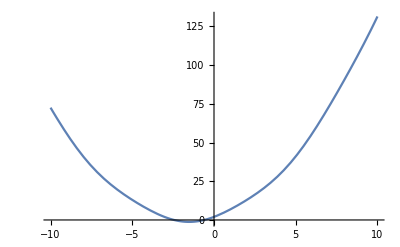

```mathematica
Plot[f[x],{x,-10,10}]
```

Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot čisto funkcijo.

```mathematica
g:=#^2+3#+2+Sin[#]&
```

#1^2+3 #1+2+Sin[#1]&

```mathematica
g[1]
```

6+Sin[1]

```mathematica
ClearAll
```

ClearAll

Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot čisto funkcijo.

```mathematica
h[x_,y_]:=(f[x]+g[y])^2
```

SetDelayed::write: Tag Integer in 5[x_,y_] is Protected.

5[1]

```mathematica
ClearAll
```

ClearAll

## Naloga 5

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[f,g]
```

Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.

```mathematica
f[x_]:=x^3+x+1;
g[n_]:=Mod[n,7]
```

Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.

```mathematica
seznam =Table[f[x],{x,0,100}]
```

{1,3,11,31,69,131,223,351,521,739,1011,1343,1741,2211,2759,3391,4113,4931,5851,6879,8021,9283,10671,12191,13849,15651,17603,19711,21981,24419,27031,29823,32801,35971,39339,42911,46693,50691,54911,59359,64041,68963,74131,79551,85229,91171,97383,103871,110641,117699,125051,132703,140661,148931,157519,166431,175673,185251,195171,205439,216061,227043,238391,250111,262209,274691,287563,300831,314501,328579,343071,357983,373321,389091,405299,421951,439053,456611,474631,493119,512081,531523,551451,571871,592789,614211,636143,658591,681561,705059,729091,753663,778781,804451,830679,857471,884833,912771,941291,970399,1000101}

```mathematica
Select[seznam,g[#]==3&]
```

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

## Naloga 6

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2 
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

```mathematica
#1^2+#2^2&[3,4]
```

25

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode s pomočjo uporabe anonimnih funkcij. Poskusi najti kodo, ki vsebuje le 1 vrstico.

```mathematica
#1[#2,#3] &[#2^2+#^2&,3,4]
```

25

## Naloga 7

Nariši graf funkcije f(x,y,z) = x sin(xy) cos(xy+z), kjer za četrto dimenzijo (z-koordinato) uporabi slider.

```mathematica
Clear[f,g,x,y,z]
```

```mathematica
f[x_,y_,z_]:=x Sin[x y]Cos[x y +z]
```

```mathematica
Manipulate[Plot3D[f[x ,y,z],{x,-10,10},{y,-10,10}],{z,-10,10}]
```

## Naloga 8

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

```mathematica
seznam = Table[Range[1,100],2]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}

```mathematica
dvojniseznam[n_]:=Table[Range[1,n],2]
```

```mathematica
dvojniseznam[6]
```

{{1,2,3,4,5,6},{1,2,3,4,5,6}}

Kaj vrne naslednja koda? Pojasni!

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

```mathematica
Krogi[4]
```

{RGBColor[1, 0, 0],Disk[{2,0}],Disk[{4,0}],Disk[{6,0}],Disk[{8,0}]}

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[n,x,y,f,g]
```

```mathematica
narisikroge[n_]:= Join[Disk[{Red}],n]
```

```mathematica
narisikroge[3]
```

Disk[{RGBColor[1, 0, 0]}]

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v rani vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato. Dodatno: ugotovi ali se da posplošiti na poljubno število krogel.

-Graphics3D-

```mathematica
Graphics3D[{Sphere[{0,y1,0}]}]
```

## Naloga 9

Implementiraj algoritem bubble sort za urejanje danega seznama. Napiši esej v katerem izraziš svojo frustracijo nad to nalogo in omeni vsaj 10 drugih programskih jezikov, ki so bolj primerni za takšne stvari.